```mathematica
H[x_]:=-x Log2[x]-(1-x) Log2[1-x] (*Shannon entropy*)
```

```mathematica
F[C_]:=1/2(1+Sqrt[1-C^2])
```

```mathematica
H[F[C]] (*Entanglement*)
```

Entanglement H[1/2 (1+√(1-C^2))]

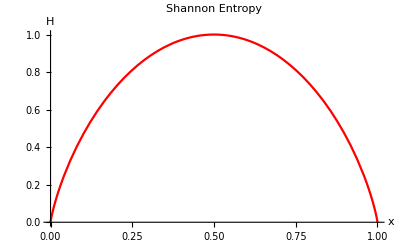

```mathematica
Plot[H[x],{x,0,1}, PlotLabel->"Shannon Entropy", AxesLabel->{x, H}, PlotStyle->Red]
```

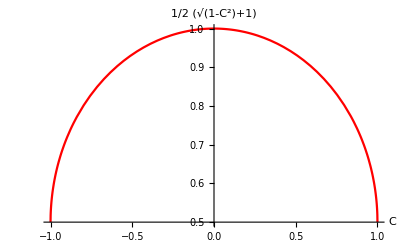

```mathematica
Plot[F[C],{C,-1,1},PlotStyle->Red, AxesLabel->Automatic, PlotLabel->F[C]]
```

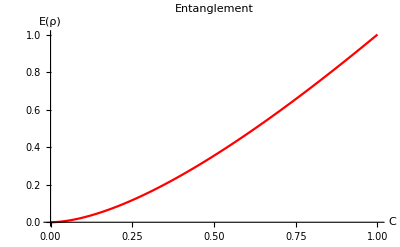

```mathematica
Plot[H[F[C]],{C,0,1}, PlotLabel->"Entanglement", PlotStyle->Red, AxesLabel->{C,"E(ρ)"}]
```

```mathematica
Entanglement[C_]:=H[F[C]]
```

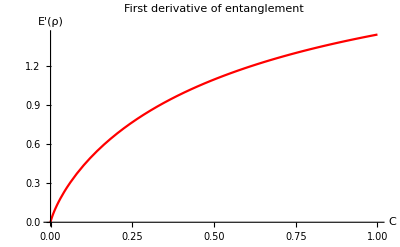

```mathematica
Plot[Entanglement'[C], {C,0,1}, PlotLabel->"First derivative of entanglement", PlotStyle->Red, AxesLabel->{C, "E'(ρ)"}]
```

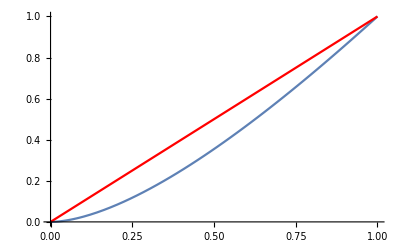

```mathematica
Show[
Plot[Ent[F[CC]],{CC,0,1}(*entanglement of formation*)],
Plot[CC,{CC,0,1},PlotStyle->Red](*concurrence*)
,Axes->True]
```

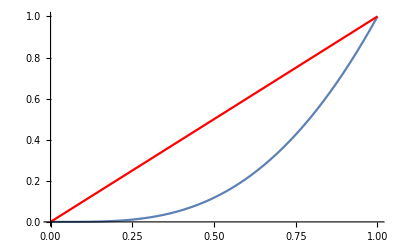

```mathematica
Show[
Plot[Ent[F[CC^2]],{CC,0,1}(*entanglement of formation*)],
Plot[CC,{CC,0,1},PlotStyle->Red](*concurrence*)
,Axes->True]
```